```mathematica
f[x_]:=155/72 x^2+113/72 x^3-37/288 x^4;
fp[x_]:=f'[x];
g[x_]:=50x;
gp[x_]:=g'[x];
road=Graphics[Join[{Gray,Thickness[Large],Line[{{0,0},{500,0}}]},Flatten[Table[{Gray,Line[{{i,-5},{i,5}}],Black,Text[ToString[i],{i,-15}]},{i,0,500,100}]]]];
meter=With[{mx=250,my=-300,mr=200},
Graphics[Join[{Black,Circle[{mx,my},mr,{0,Pi}]},Table[Line[{{mx,my}+mr{Cos[θ],Sin[θ]},{mx,my}+(mr-10){Cos[θ],Sin[θ]}}],{θ,0,Pi,Pi/10}],Table[Text[ToString[10i],{mx,my}+(mr+15){Cos[(Pi (10-i))/10],Sin[(Pi(10-i))/10]}],{i,0,10}]]]
];
```

```mathematica
Animate[Module[{car,dial,x0=-15,x1=515,y0=-310,y1=30,mx=250,my=-300,mr=200},
car=Graphics[{Red,Disk[{g[t],0},10]}];
dial=Graphics[{Red,Thickness[Medium],Arrow[{{mx,my},{mx,my}+0.75mr{Cos[Pi(1-gp[t]/100)],Sin[Pi(1-gp[t]/100)]}}]}];
Show[road,car,meter,dial,PlotRange->{{x0,x1},{y0,y1}}]
],{t,0,10,Appearance->"Labeled"},AnimationRunning->False,AnimationRate->2]
```

```mathematica
Animate[Module[{car,dial,x0=-15,x1=515,y0=-310,y1=30,mx=250,my=-300,mr=200},
car=Graphics[{Red,Disk[{f[t],0},10]}];
dial=Graphics[{Red,Thickness[Medium],Arrow[{{mx,my},{mx,my}+0.75mr{Cos[Pi(1-fp[t]/100)],Sin[Pi(1-fp[t]/100)]}}]}];
Show[road,car,meter,dial,PlotRange->{{x0,x1},{y0,y1}}]
],{t,0,10,Appearance->"Labeled"},AnimationRunning->False,AnimationRate->2]
```

```mathematica
Manipulate[Module[{t1=6.0,car1,car2,estimate,x0=-15,x1=515,y0=-310,y1=30,mx=250,my=-300,mr=200,v,vtext},
car1=Graphics[{Red,Disk[{f[t1],0},10]}];
car2=Graphics[{Orange,Disk[{f[t2],0},10]}];
v=If[t1≠t2,N[(f[t2]-f[t1])/(t2-t1)],Infinity];
vtext=Graphics[{Black,Text[Style["v_avg = Δs/Δt = s_2/t_2 = "<>If[v<Infinity,ToString[v],"undefined"],16],{Mean[{x0,x1}],Mean[{y0,y1}]}]}];
Show[road,car1,car2,vtext,PlotRange->{{x0,x1},{y0,y1}}]
],{t2,0,10,0.1,Appearance->"Labeled"}]
```

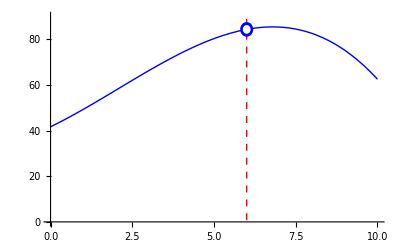

```mathematica
Show[Plot[(f[t2]-f[6])/(t2-6),{t2,0,10},PlotStyle->{Blue,Thick}],Graphics[{Red,Dashed,Thick,InfiniteLine[{6,0},{0,1}],Blue,Disk[{6,fp[6]},{0.2,3.2}],White,Disk[{6,fp[6]},{0.6*0.2,0.6*3.2}]}],PlotRange->{0,90},AxesOrigin->{0,0}]
```